Brian Mechanism
The cheapest way to make large scale precision robots.


Brian Onang’o
July 2022

@CSECO

```mathematica
DegreestoRadians[degree_]:=(2 Pi * degree)/360
(*Dynamic [skeleton1DoFX];
skeleton1DoFX = 0;*)
BrianMechanism1DoFSkeleton[legHeight_, robotLength_, endEffectorLength_, endEffectorHeight_, x_, workspace_, robotWidth_, fleshy_]:=Module[{

},{
compoundX = Floor[x/robotLength];
innerX = Mod[x, robotLength];
(*Frame 1*)
F1L1p1={0,0,0}; (*Frame1 Leg1 point 1*)
F1L1p2Vect = {0,0,legHeight+endEffectorHeight};
F1L1p2 =F1L1p2Vect;
robotLenVect = {robotLength,0,0};
F1L2p1=F1L1p1+robotLenVect;
F1L2p2 =F1L1p2+robotLenVect;
F1G1p1 = {0,0,legHeight};
F1G1p2 = F1G1p1+robotLenVect;

(*Frame 2*)
F2L2p2=F1L1p2; (*Frame2 Leg1 point 1*)
F2L2p1 =F2L2p2+F1L1p2Vect;

F2L1p2=F1L2p2;
F2L1p1 =F2L1p2+F1L1p2Vect;

F2G1p1 = F1G1p2+{0,0,2*endEffectorHeight};
F2G1p2 = F1G1p1+{0,0,2*endEffectorHeight};

xUnitVect = {1,0,0};
yUnitVect = {0,1,0};

(*initial frame rotations*)
rotateAllPoints[pivot_, direction_, degrees_]:={
F1L1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L1p1-pivot);
F1L1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L1p2-pivot);

F1L2p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L2p1-pivot);
F1L2p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L2p2-pivot);

F1G1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1G1p1-pivot);
F1G1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1G1p2-pivot);

F2L1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L1p1-pivot);
F2L1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L1p2-pivot);

F2L2p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L2p1-pivot);
F2L2p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L2p2-pivot);

F2G1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2G1p1-pivot);
F2G1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2G1p2-pivot);
};
rotateFrame1[pivot_, direction_, degrees_]:={
F1L1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L1p1-pivot);
F1L1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L1p2-pivot);
F1L2p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L2p1-pivot);
F1L2p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1L2p2-pivot);
F1G1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1G1p1-pivot);
F1G1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F1G1p2-pivot);
};
rotateFrame2[pivot_, direction_, degrees_]:={
F2L1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L1p1-pivot);
F2L1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L1p2-pivot);
F2L2p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L2p1-pivot);
F2L2p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2L2p2-pivot);
F2G1p1 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2G1p1-pivot);
F2G1p2 = pivot + RotationMatrix[DegreestoRadians[direction * degrees],yUnitVect].(F2G1p2-pivot);
};
pivot = {0,0,0};
rotationDirection = 0;

If[compoundX >0,
For[i=0, i <compoundX, i++,
pivot = If[Mod[i,2]==0,
  F1L2p2,(*even compoundX*)
F1L1p2 (*odd compoundX*)
];
(*Print[{x,compoundX, i, pivot, rotationDirection}];*)
rotationDirection = 1;
rotateAllPoints[pivot,rotationDirection, 180 ]
],
(*less than zero*)
If[compoundX <0,

For[i=0, i >compoundX, i--,
pivot = If[Mod[i, 2]==0,
  F1L1p2,
F1L2p2  
];
rotationDirection = -1;
rotateAllPoints[pivot,rotationDirection , 180]
],False]
];

(*rotationBoundaries*)
outerBoundaryLen = (*1/8*robotLength*)endEffectorLength;
b1p1 = If[Mod[compoundX,2]==0, F1L1p2 -{0,0,endEffectorHeight} +{outerBoundaryLen,0,0},F2L1p2 -{0,0,endEffectorHeight} +{outerBoundaryLen,0,0} ];
b1p2 = b1p1 + {1/4*robotLength,0,0};

b2p2 = If[Mod[compoundX,2]==0, F1L2p2 -{0,0,endEffectorHeight} -{outerBoundaryLen,0,0},F2L2p2 -{0,0,endEffectorHeight} -{outerBoundaryLen,0,0} ];
b2p1 = b2p2- {1/4*robotLength,0,0};


If[x <b1p1[[1]],(*before first boundary => dwell*)

pivot = If[Mod[compoundX,2]==0,
F1L1p2  ,(*even compoundX*)
F1L2p2 (*odd compoundX*)
];
rotationDirection = 1;
degreez= 0;
If[Mod[compoundX,2]==0,
  rotateFrame2[pivot,rotationDirection ,-(180- degreez)],(*even compoundX*)
 rotateFrame1[pivot,rotationDirection ,-(180- degreez)] (*odd compoundX*)
]
,
False
];

If[x≥b1p1[[1]] && b1p2[[1]] ≥ x,(*within first boundary*)

pivot = If[Mod[compoundX,2]==0,
F1L1p2  ,(*even compoundX*)
F1L2p2 (*odd compoundX*)
];
rotationDirection = 1;
degreez= (x-b1p1[[1]])/(b1p2[[1]]-b1p1[[1]])*180;
If[Mod[compoundX,2]==0,
  rotateFrame2[pivot,rotationDirection ,-(180- degreez)],(*even compoundX*)
 rotateFrame1[pivot,rotationDirection ,-(180- degreez)] (*odd compoundX*)
]
,
False
];

If[x≥b2p1[[1]] && b2p2[[1]] ≥ x,(*within second boundary*)

pivot = If[Mod[compoundX,2]==0,
F1L2p2  ,(*even compoundX*)
 F1L1p2 (*odd compoundX*)
];
rotationDirection = 1;
degreez= (b2p2[[1]]-x)/(b2p2[[1]]-b2p1[[1]])*180;
If[Mod[compoundX,2]==0,
  rotateFrame2[pivot,rotationDirection ,(180- degreez)],(*even compoundX*)
 rotateFrame1[pivot,rotationDirection ,(180- degreez)] (*odd compoundX*)
]
,
False
];


If[x > b2p2[[1]],(*after 2nd boundary => dwell*)

pivot = If[Mod[compoundX,2]==0,
F1L2p2  ,(*even compoundX*)
F1L1p2  (*odd compoundX*)
];
rotationDirection = 1;
degreez= 0;
If[Mod[compoundX,2]==0,
  rotateFrame2[pivot,rotationDirection ,(180- degreez)],(*even compoundX*)
 rotateFrame1[pivot,rotationDirection ,(180- degreez)] (*odd compoundX*)
]
,
False
];
F1BL1p1 = F1L1p1;
F1BL1p2 = F1L1p2;
F1BL2p1 = F1L2p1;
F1BL2p2 = F1L2p2;
F1BG1p1 = F1G1p1;
F1BG1p2 = F1G1p2;

F2BL1p1=F2L1p1;
F2BL1p2=F2L1p2;
F2BL2p1=F2L2p1;
F2BL2p2=F2L2p2;
F2BG1p1=F2G1p1;
F2BG1p2=F2G1p2;

frame1Leg1Points= {F1L1p1, F1L1p2};
frame1Leg2Points= {F1L2p1, F1L2p2};
frame1GantryPoints= {F1G1p1, F1G1p2};

frame2Leg1Points= {F2L1p1, F2L1p2};
frame2Leg2Points= {F2L2p1, F2L2p2};
frame2GantryPoints= {F2G1p1, F2G1p2};




endEffectorPoints = {
{
x-endEffectorLength/2,0,legHeight-endEffectorHeight/2
},
{
x+endEffectorLength/2,0,legHeight+endEffectorHeight/2
}
};
endEffectorBPoints = endEffectorPoints;
If[robotWidth>0,(*3D*)
F1BL1p1[[2]]=robotWidth;
F1BL1p2[[2]]=robotWidth;
F1BL2p1[[2]]=robotWidth;
F1BL2p2[[2]]=robotWidth;
F1BG1p1[[2]]=robotWidth;
F1BG1p2[[2]]=robotWidth;

F2BL1p1[[2]]=robotWidth;
F2BL1p2[[2]]=robotWidth;
F2BL2p1[[2]]=robotWidth;
F2BL2p2[[2]]=robotWidth;
F2BG1p1[[2]]=robotWidth;
F2BG1p2[[2]]=robotWidth;

endEffectorBPoints[[1]][[2]] = robotWidth;
endEffectorBPoints[[2]][[2]] = robotWidth;
];

frame1BLeg1Points={F1BL1p1,F1BL1p2};
frame1BLeg2Points={F1BL2p1,F1BL2p2};
frame1BGantryPoints={F1BG1p1,F1BG1p2};
frame2BLeg1Points={F2BL1p1,F2BL1p2};
frame2BLeg2Points={F2BL2p1,F2BL2p2};
frame2BGantryPoints={F2BG1p1,F2BG1p2};

gantryPoints = {
endEffectorPoints[[1]]+(endEffectorPoints[[2]]-endEffectorPoints[[1]])/2,
endEffectorBPoints[[1]]+(endEffectorBPoints[[2]]-endEffectorBPoints[[1]])/2
};


worksSpaceInc = Sqrt[(legHeight+endEffectorHeight)^2 + robotLength^2];
(*F13Dp1 = endEffectorPoints[[1]];F13Dp1[[1]]=F1L1p1[[1]];F13Dp2[[2]]-=50;*)
F13Dp1 = F1G1p1;F13Dp1[[2]]-=50;
F13Dp2 = F1G1p2;F13Dp2[[2]]-=50;
F1B3Dp1 = F1BG1p1;F1B3Dp1[[2]]-=50;
F1B3Dp2 = F1BG1p2;F1B3Dp2[[2]]-=50;
F23Dp1=F2G1p1;F23Dp1[[2]]-=50;
F23Dp2=F2G1p2;F23Dp2[[2]]-=50;
F2B3Dp1=F2BG1p1;F2B3Dp1[[2]]-=50;
F2B3Dp2=F2BG1p2;F2B3Dp2[[2]]-=50;
{
Thick,
Green, Line[frame1Leg1Points];Line[ frame1Leg2Points]; Line[frame1GantryPoints];Cylinder[{F1L1p1,F1L1p2},If[fleshy==True,50,0]],Cylinder[{F1L2p1,F1L2p2},If[fleshy==True,50,0]],

Red, Line[frame2Leg1Points];Line[ frame2Leg2Points]; Line[frame2GantryPoints];Cylinder[{F2L1p1,F2L1p2},If[fleshy==True,50,0]],Cylinder[{F2L2p1,F2L2p2},If[fleshy==True,50,0]],

Green,Line[frame1BLeg1Points];Line[frame1BLeg2Points];Line[frame1BGantryPoints];Cylinder[{F1BL1p1,F1BL1p2},If[fleshy==True,50,0]],Cylinder[{F1BL2p1,F1BL2p2},If[fleshy==True,50,0]],

Red,Line[frame2BLeg1Points];Line[frame2BLeg2Points];Line[frame2BGantryPoints]; Cylinder[{F2BL1p1,F2BL1p2},If[fleshy==True,50,0]],Cylinder[{F2BL2p1,F2BL2p2},If[fleshy==True,50,0]],


Cyan, Cuboid[endEffectorPoints[[1]],endEffectorPoints[[2]] ], Cuboid[endEffectorBPoints[[1]],endEffectorBPoints[[2]] ],
Black, Line[gantryPoints],
Black, Line[{{workspace[[1]]-worksSpaceInc,0,0},{workspace[[2]]+worksSpaceInc,0,0}}], Line[{{workspace[[1]],0,0},{workspace[[1]],0,F1L1p2Vect[[3]]+worksSpaceInc}}],
Cuboid[endEffectorPoints[[1]],If[fleshy==True,endEffectorBPoints[[2]],endEffectorPoints[[2]]]],
Cyan,Cylinder[{F13Dp1,F13Dp2},If[fleshy==True,50,0]],Cylinder[{F1B3Dp1,F1B3Dp2},If[fleshy==True,50,0]],
Red,Cylinder[{F23Dp1,F23Dp2},If[fleshy==True,50,0]],Cylinder[{F2B3Dp1,F2B3Dp2},If[fleshy==True,50,0]],
Yellow, Cuboid[endEffectorPoints[[1]],endEffectorBPoints[[2]]];

}

}]
```

```mathematica
BrianMechanismConcept1DoFSqWheel[wheelLen_, endEffectorLength_, t_ ]:=Module[
{
numRotations = Floor [t/(wheelLen*2)],
numLengths = Floor [t/wheelLen],
innerX = Mod[t, wheelLen]


},{
innerX = If[Mod[numLengths, 2]==0,innerX, wheelLen - innerX]; (*End effector resetting to zero*)
(*numRotations1 -=If[innerX == wheelLen,1,0];*)
(*x = numRotations  * wheelLen + If[Mod[numRotations, 2]==1,0, innerX];*)
(*x = wheelLen + Floor [numRotations/2]* wheelLen + If[Mod[numRotations, 2]==1,innerX, 0]; *)
x =  Floor [numLengths/2]* wheelLen + If[Mod[numLengths, 2]==0,innerX, wheelLen]; 
wheelCenter = {(numRotations(*-If[numRotations>0,1,0]*))*wheelLen,0} + {wheelLen/2, wheelLen/2};(* - If[numRotations>0,0,1]*{wheelLen,0}; *)
(*New*)
wheelCenterX0 = (numRotations )*(wheelLen * 2) + wheelLen;
wheelCenterX = wheelCenterX0+If[t >(wheelCenterX0+wheelLen/2), wheelLen/2, -wheelLen/2];
wheelCenterX = {wheelLen/2 + Floor[t/(wheelLen*2)]*wheelLen,wheelLen/2};
(*wheelCenter = {wheelCenterX, wheelLen/2 };*)
wheelCenter = wheelCenterX;

pivot = wheelCenter+{wheelLen/2,-wheelLen/2};
wheelRadius = Sqrt[ 2*wheelLen/2* wheelLen/2];
wheelCenter =pivot+ If[Mod[numLengths, 2]==0,wheelCenter-pivot,  RotationMatrix[(45+innerX/wheelLen*90) Degree].({wheelRadius,0} )];
wheelCenter2 = wheelCenter+ {2 * wheelLen/2+wheelLen + endEffectorLength,0};
ganPoint1 = wheelCenter - {wheelLen/8, wheelLen/8}; 
ganPoint2 = wheelCenter2 + {wheelLen/8, wheelLen/8}; 
rotationAngle =If[Mod[numLengths,2]!=0,(innerX/wheelLen*90) Degree,0] ;
endEffectorPoint1 = wheelCenter + {wheelLen/2+innerX,-wheelLen/4};
endEffectorPoint2 =endEffectorPoint1+{endEffectorLength, wheelLen/2};


{t, x, innerX},
wheelCenter,
Graphics[{

Line[{{0,0},{700, 0}}],
Line[{{0,0},{0,100}}],
(*Cyan, Rotate[Rectangle[wheelCenter2+{-wheelLen/2,-wheelLen/2},wheelCenter2+{wheelLen/2,wheelLen/2}],rotationAngle, wheelCenter2],
Yellow,Rotate[Rectangle[wheelCenter+{-wheelLen/2,-wheelLen/2},wheelCenter+{wheelLen/2,wheelLen/2}],rotationAngle, wheelCenter],*)
Red, Rectangle[ganPoint1, ganPoint2],
Black, Rectangle[endEffectorPoint1, endEffectorPoint2],

Thick, Green, Rotate[Line[{wheelCenter+{-wheelLen/2,-wheelLen/2},wheelCenter+{wheelLen/2,wheelLen/2}}],rotationAngle, wheelCenter],
Rotate[Line[{wheelCenter+{-wheelLen/2,wheelLen/2},wheelCenter+{wheelLen/2,-wheelLen/2}}],rotationAngle, wheelCenter],
Thick, Black, Rotate[Line[{wheelCenter2+{-wheelLen/2,-wheelLen/2},wheelCenter2+{wheelLen/2,wheelLen/2}}],rotationAngle, wheelCenter2],
Rotate[Line[{wheelCenter2+{-wheelLen/2,wheelLen/2},wheelCenter2+{wheelLen/2,-wheelLen/2}}],rotationAngle, wheelCenter2]
}]
}]
```

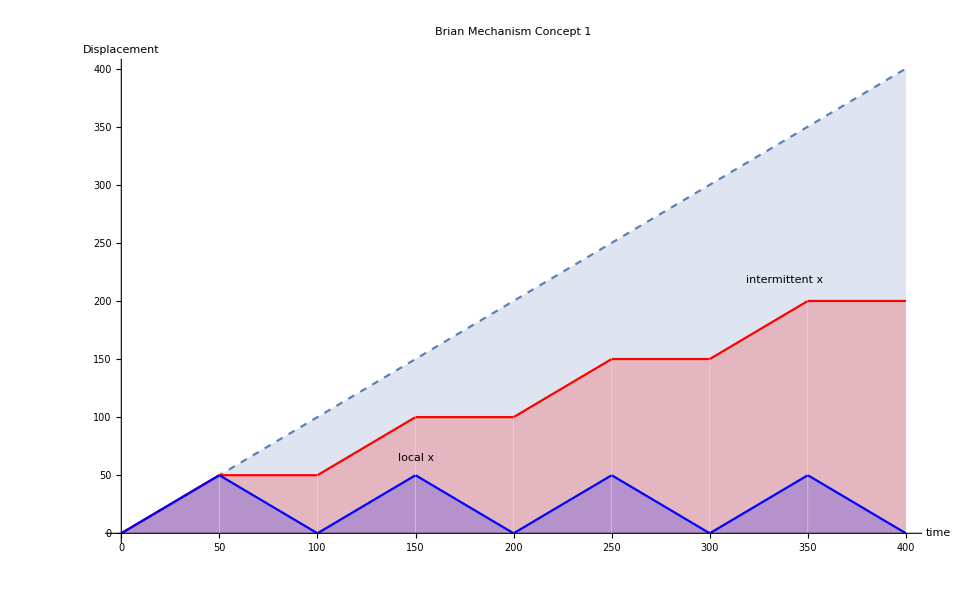

```mathematica
Plot[{BrianMechanismConcept1DoFSqWheel[50,10,t][[1]][[1]],BrianMechanismConcept1DoFSqWheel[50,10,t][[1]][[2]], BrianMechanismConcept1DoFSqWheel[50,10,t][[1]][[3]]},{t,0,400},Filling->Axis,AxesLabel->{"time", "Displacement"}, PlotLabels->Placed[{"continuous x","intermittent x","local x"},Above],PlotStyle->{Dashed, Red, Blue}, PlotLabel->"Brian Mechanism Concept 1"]
```

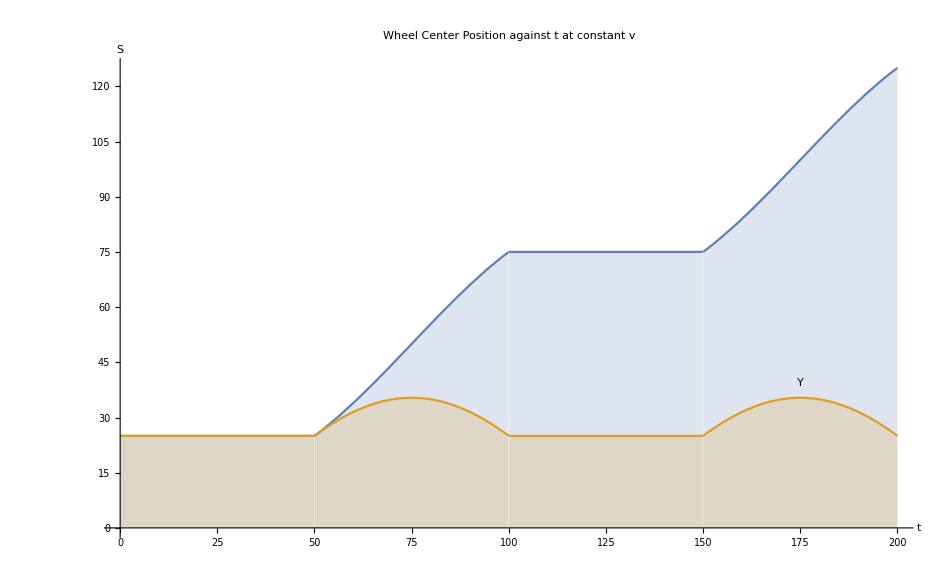

```mathematica
Plot[{BrianMechanismConcept1DoFSqWheel[50,10,t][[2]][[1]],BrianMechanismConcept1DoFSqWheel[50,10,t][[2]][[2]]},{t,0,200}, AxesLabel->{"t","S"}, PlotLabels->Placed[{"X","Y"},Above], PlotLabel-> "Wheel Center Position against t at constant v", Filling->Axis, AxesOrigin->{0,0}]
```

First Mechanism
intermittent motion

```mathematica
Animate[
BrianMechanismConcept1DoFSqWheel[50,10,t][[3]]
,{t,0,500,Appearance->"Labeled"},Initialization:>{t=0, start=0, stop=700}, AnimationRunning->False, AnimationDirection->ForwardBackward,AnimationRate->10]
```

Second Mechanism

```mathematica
Animate[
Graphics3D[
{
BrianMechanism1DoFSkeleton[1000,2000,300,100,x, {start,stop},2000, True]
}, Axes-> False, AxesLabel->{"X","Y", "Z"}(*, ViewPoint->Top*)
],{x,-10000,10000,Appearance->"Labeled"},Initialization:>{x=0, start=-10000, stop=10000}, AnimationRunning->False, AnimationDirection->ForwardBackward,AnimationRate->300]
```

Actual Working Mechanism
Loading...